```mathematica
Join[{a},{{b},{c},{d}}]
```

{a,{b},{c},{d}}

```mathematica
Flatten[{{a},{b,c,d}},1]
```

{a,b,c,d}

```mathematica
baseDir="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\voltage"
For[i=225,i≤325,i+=25,
CreateDirectory[StringJoin[baseDir,"\\Stitched","\\","V",ToString[i]]]]
```

C:\Users\maruk\Desktop\Research\PHY242\retake\voltage

```mathematica
namingConvention[voltage_,region_]:=Module[{name,names,scaled},
name = StringJoin[ToString[voltage],"R", ToString[region],".txt"];
scaled = StringJoin[ToString[voltage],"R", ToString[region],"scaled",".txt"];
names = {name,scaled};
Return[names]]
```

```mathematica
(*
ScaledDirectory is the location of the scaled files. FinalDirectory is where your files will be saved. 
You will have to change these to your directories.
You will have to create the final directory folder for the output files.
*)
ScaledDirectory="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\voltage_scaled";
FinalDirectory="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\voltage\\Stitched\\V225";
SetDirectory[ScaledDirectory];
FileNames[]
```

{225R1scaled.txt,225R2scaled.txt,225R3scaled.txt,225R4scaled.txt,225R5scaled.txt,225R6scaled.txt,225R7scaled.txt,250R1scaled.txt,250R2scaled.txt,250R3scaled.txt,250R4scaled.txt,250R5scaled.txt,250R6scaled.txt,250R7scaled.txt,275R1scaled.txt,275R2scaled.txt,275R3scaled.txt,275R4scaled.txt,275R5scaled.txt,275R6scaled.txt,275R7scaled.txt,300R1scaled.txt,300R2scaled.txt,300R3scaled.txt,300R4scaled.txt,300R5scaled.txt,300R6scaled.txt,300R7scaled.txt,325R1scaled.txt,325R2scaled.txt,325R3scaled.txt,325R4scaled.txt,325R5scaled.txt,325R6scaled.txt,325R7scaled.txt}

```mathematica
d1 = Import["225R4scaled.txt","Table"];
d2=Import["225R5scaled.txt","Table"];
```

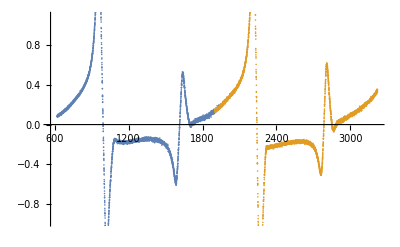

```mathematica
ListPlot[{d1[[All,{1,3}]],d2[[All,{1,3}]]}]
```

```mathematica
massImport[numRegions_,val_]:=Module[{dataList,i,name,data},
dataList={};
For[i=1,i≤numRegions,i++,
name=namingConvention[val,i][[2]];
data=Import[name,"Table"];
AppendTo[dataList,data]];
Return[dataList]]
```

```mathematica
data225=massImport[7,225];
```

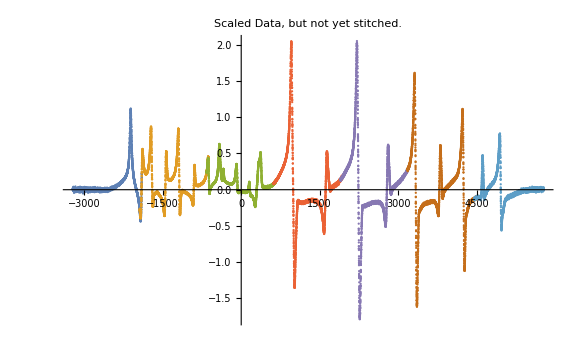

```mathematica
ListPlot[data225[[All,All,{1,3}]],ImageSize->Large,PlotLabel->"Scaled Data, but not yet stitched.",PlotRange->All]
```

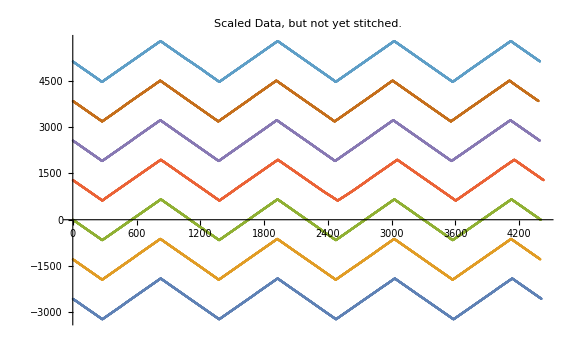

```mathematica
ListPlot[data225[[All,All,1]],ImageSize->Large,PlotLabel->"Scaled Data, but not yet stitched."]
```

```mathematica
(*This function finds the max and min for each file. These are used in the next function to cut the data*)
subset=1100;
NumOfSubsets=Ceiling[1/subset Min[{Length[data225[[1]]],Length[data225[[2]]],Length[data225[[3]]],Length[data225[[4]]],Length[data225[[5]]],Length[data225[[6]]],Length[data225[[7]]]}]];
maxmin[data_,subset_]:=Module[{},
dt=Partition[data[[All,1]],subset,subset,1,{}];
max=Flatten[Table[{Position[data[[All,1]],Max[dt[[i]]]]},{i,1,NumOfSubsets}]];
min=Flatten[Table[{Position[data[[All,1]],Min[dt[[i]]]]},{i,1,NumOfSubsets}]];
(*max=Flatten[Join[dt[[All,1]],Position[data[[All,1]],Max[data[[subset (NumOfScans-1);;subset (NumOfScans),1]]]]]];
min=Flatten[Join[dt[[All,2]],Position[data[[All,1]],Min[data[[subset (NumOfScans-1);;-1,1]]]]]];*)
{max,min}
];
```

```mathematica
(*Finds all the maximums and minimums for the data file*) 
{max1,min1}=maxmin[data225[[1]],subset];
{max2,min2}=maxmin[data225[[2]],subset];
{max3,min3}=maxmin[data225[[3]],subset];
{max4,min4}=maxmin[data225[[4]],subset];
{max5,min5}=maxmin[data225[[5]],subset];
{max6,min6}=maxmin[data225[[6]],subset];
{max7,min7}=maxmin[data225[[7]],subset];
```

Check to make sure everything worked.  The gridlines should be at every turning point.

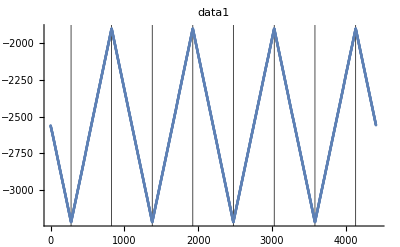

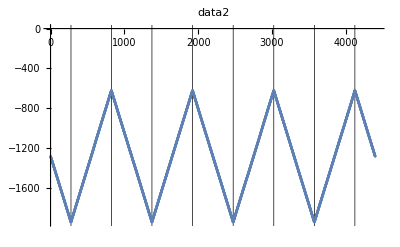

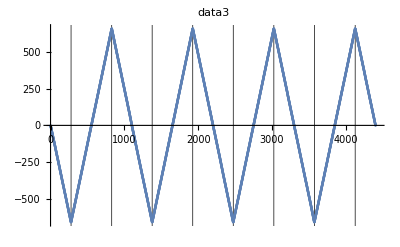

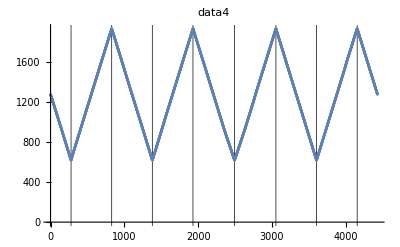

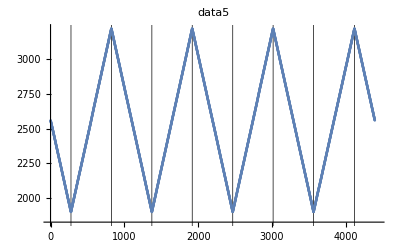

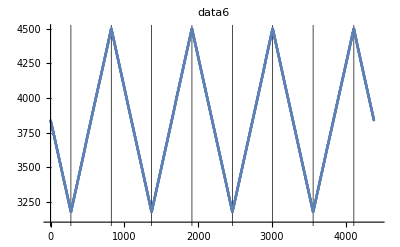

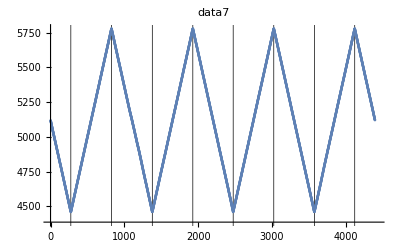

```mathematica
Print["Check to make sure everything worked.  The gridlines should be at every turning point."];
plotmax=Max[{Length[data225[[1]]],Length[data225[[2]]],Length[data225[[3]]],Length[data225[[4]]],Length[data225[[5]]],Length[data225[[6]]],Length[data225[[7]]]}];
ListPlot[data225[[1,All,1]],GridLines->{Join[max1,min1],None},GridLinesStyle->Black,PlotLabel->"data1",PlotRange->{{0,plotmax},Automatic}]
ListPlot[data225[[2,All,1]],GridLines->{Join[max2,min2],None},GridLinesStyle->Black,PlotLabel->"data2",PlotRange->{{0,plotmax},Automatic}]
ListPlot[data225[[3,All,1]],GridLines->{Join[max3,min3],None},GridLinesStyle->Black,PlotLabel->"data3",PlotRange->{{0,plotmax},Automatic}]
ListPlot[data225[[4,All,1]],GridLines->{Join[max4,min4],None},GridLinesStyle->Black,PlotLabel->"data4",PlotRange->{{0,plotmax},Automatic}]
ListPlot[data225[[5,All,1]],GridLines->{Join[max5,min5],None},GridLinesStyle->Black,PlotLabel->"data5",PlotRange->{{0,plotmax},Automatic}]
ListPlot[data225[[6,All,1]],GridLines->{Join[max6,min6],None},GridLinesStyle->Black,PlotLabel->"data6",PlotRange->{{0,plotmax},Automatic}]
ListPlot[data225[[7,All,1]],GridLines->{Join[max7,min7],None},GridLinesStyle->Black,PlotLabel->"data7",PlotRange->{{0,plotmax},Automatic}]
```

```mathematica
(*This function splits a data file into 10 scan ups and 10 scan downs*)
split[data_,max_,min_]:=Module[{},
up={};
For[i=1,i<=Length[max],
up=Join[up,{data[[min[[i]];;max[[i]]]]}];
i++;];

down={};
For[i=1,i<=Length[max]-1,
down=Join[down,{Reverse[data[[max[[i]];;min[[i+1]]]]]}];
i++;];
If[Length[max]==10,down=Join[down,{Reverse[Join[data[[Last[max];;-1]],data[[1;;min[[1]]]]]]}];];
{up,down}
];
```

```mathematica
(*run split function for all 4 data files*)
{up1,down1}=split[data225[[1]],max1,min1];
{up2,down2}=split[data225[[2]],max2,min2];
{up3,down3}=split[data225[[3]],max3,min3];
{up4,down4}=split[data225[[4]],max4,min4];
{up5,down5}=split[data225[[5]],max5,min5];
{up6,down6}=split[data225[[6]],max6,min6];
{up7,down7}=split[data225[[7]],max7,min7];
```

```mathematica
(*Check to make sure all up data is correct.  The data is still not stiched
Use this cell to find out how many scanups we have
*)
Manipulate[ListPlot[{up1[[i]][[All,{1,3}]],up2[[i]][[All,{1,3}]],up3[[i]][[All,{1,3}]],up4[[i]][[All,{1,3}]],up7[[i]][[All,{1,3}]],up6[[i]][[All,{1,3}]],up5[[i]][[All,{1,3}]]},ImageSize->Large],{i,1,Length[up1],1}]
```

```mathematica
(*Check to make sure all down data is correct.  The data is still not stiched

Use this cell to find out how many scandowns we have
*)
Manipulate[ListPlot[{down1[[i]][[All,{1,3}]],down2[[i]][[All,{1,3}]],down3[[i]][[All,{1,3}]],down4[[i]][[All,{1,3}]],down5[[i]][[All,{1,3}]],down6[[i]][[All,{1,3}]],down7[[i]][[All,{1,3}]]},ImageSize->Large],{i,1,Length[down1],1}]
```

```mathematica
(*You need to change these to match the number of up scans and down scans you have from the above plots*) 
NumOfUpScans=4;
NumOfDownScans=3;
```

```mathematica
shifty[in_]:=Module[{holds,length,i,mid,shifts,ya,yb,shift,hold,j,subtract,out},
holds ={};
shifts={};
out=in[[1]];
length = Length[in];
For[i=1,i≤length-1,i++,
mid = Mean[Flatten[{Select[in[[i]],#[[1]]>=Floor[in[[i+1]][[1,1]]]&][[All,1]],Select[in[[i+1]],#[[1]]<=Ceiling[in[[i]][[-1,1]]]&][[All,1]]}]];
ya=LinearModelFit[Select[in[[i]],#[[1]]>=Floor[in[[i+1]][[1,1]]]&][[All,{1,3}]],x,x];
yb=LinearModelFit[Select[in[[i+1]],#[[1]]<=Ceiling[in[[i]][[-1,1]]]&][[All,{1,3}]],x,x];
shift=ya[mid]-yb[mid];
AppendTo[shifts,shift];
hold =in[[i+1]];
subtract=0;
For[j=1,j≤i,j++,
subtract+=shifts[[j]]];
hold[[All,3]]=in[[i+1]][[All,3]]-subtract;
out=Join[out,hold]];
out]
```

```mathematica
(*Stiching function*)
shifty[in1_,in2_,in3_,in4_]:=Module[{},
mid12=Mean[Flatten[{Select[in1,#[[1]]>=Floor[in2[[1,1]]]&][[All,1]],Select[in2,#[[1]]<=Ceiling[in1[[-1,1]]]&][[All,1]]}]];
y12a=LinearModelFit[Select[in1,#[[1]]>=Floor[in2[[1,1]]]&][[All,{1,3}]],x,x];
y12b=LinearModelFit[Select[in2,#[[1]]<=Ceiling[in1[[-1,1]]]&][[All,{1,3}]],x,x];

mid23=Mean[Flatten[{Select[in2,#[[1]]>=Floor[in3[[1,1]]]&][[All,1]],Select[in3,#[[1]]<=Ceiling[in2[[-1,1]]]&][[All,1]]}]];
y23a=LinearModelFit[Select[in2,#[[1]]>=Floor[in3[[1,1]]]&][[All,{1,3}]],x,x];
y23b=LinearModelFit[Select[in3,#[[1]]<=Ceiling[in2[[-1,1]]]&][[All,{1,3}]],x,x];

mid34=Mean[Flatten[{Select[in3,#[[1]]>=Floor[in4[[1,1]]]&][[All,1]],Select[in4,#[[1]]<=Ceiling[in3[[-1,1]]]&][[All,1]]}]];
y34a=LinearModelFit[Select[in3,#[[1]]>=Floor[in4[[1,1]]]&][[All,{1,3}]],x,x];
y34b=LinearModelFit[Select[in4,#[[1]]<=Ceiling[in3[[-1,1]]]&][[All,{1,3}]],x,x];

shift12=y12b[mid12]-y12a[mid12];
shift23=y23b[mid23]-y23a[mid23];
shift34=y34b[mid34]-y34a[mid34];

hold2=in2;
hold2[[All,3]]=in2[[All,3]]-shift12;
hold3=in3;
hold3[[All,3]]=in3[[All,3]]-shift12-shift23;
hold4=in4;
hold4[[All,3]]=in4[[All,3]]-shift12-shift23-shift34;

out=Join[in1,hold2,hold3,hold4];
out
]
```

```mathematica
(*Check to make sure all up data is correct.  The data is still now stiched*)
Manipulate[ListLinePlot[Evaluate[shifty[{up1[[i]],up2[[i]],up3[[i]],up4[[i]],up5[[i]],up6[[i]],up7[[i]]}]][[All,{1,3}]],PlotRange->All],{i,1,4,1}]
```

```mathematica
(*Check to make sure all down data is correct.  The data is still now stiched*)
Manipulate[ListLinePlot[Evaluate[shifty[{down1[[i]],down2[[i]],down3[[i]],down4[[i]],down5[[i]],down6[[i]],down7[[i]]}]][[All,{1,3}]],PlotRange->All],{i,1,NumOfDownScans,1}]
```

```mathematica
(*Export final data*)
SetDirectory[FinalDirectory]
For[i=1,i<=NumOfUpScans,
upfinal=shifty[{up1[[i]],up2[[i]],up3[[i]],up4[[i]],up5[[i]],up6[[i]],up7[[i]]}];
FN="scanup"<>If[i<10,"0"<>ToString[i],ToString[i]]<>".txt";
Export[FN,upfinal,"Table"];
i++;];
For[i=1,i<=NumOfDownScans,
downfinal=shifty[{down1[[i]],down2[[i]],down3[[i]],down4[[i]],down5[[i]],down6[[i]],down7[[i]]}];
FN="scandown"<>If[i<10,"0"<>ToString[i],ToString[i]]<>".txt";
Export[FN,downfinal,"Table"];
i++;];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\voltage\Stitched\V225